# The Pseudo-Potential Method

## Jeremy Jorgensen

The pseudo-potential being constructed is simply a toy model and doesn’t correspond to any physical system. The pseudo-potential method is described in Grosso, http://journals.aps.org/pr/absutract/10.1103/PhysRev.116.555.

### Pseudo-Potential Method

From Grosso, the electronic valence and conduction states are obtained from the solution of the characteristic equation,

||(k_i^2-E)δ_ij+∑_d_ν e^(-i(h_i-h_j) ·d_ν)V_ν^(pseudo)(h_i-h_j)||=0,

where h_i are reciprocal lattice vectors, k_i=k+h_i, k_i^2 are the empty lattice kinetic energies, k is a chosen wave vector from the Brillouin zone, h_i are reciprocal lattice vectors, d_ν is an atomic basis vector, V_ν^(pseudo)(h_i-h_j) are the pseudo-potential form factors, and e^(-i(h_i-h_j)·d_ν) are the structure phase factors.

If we assume that the atomic basis consists of one atom at the origin, the structure phase factor disappears and the characteristic equation simplifies to

||(k_i^2-E)δ_ij+V_ν^(pseudo)(h_i-h_j)||=0.

We only allow the first two shells of a simple cubic lattice contribute to the form factors. If we set the lattice constant, a, to 2π, these shells are then located at [±1,0,0] and [±1,±1,0] along with permutations of both. The pseudo-potential form factors are then given by V_ν^(pseudo)(1) = V_1 and V_ν^(pseudo)(√2)=V_2. The pseudo-potential form factors are spherical isosurfaces.

## Pseudo-Potential Construction

```mathematica
kv[bv_,R_]:=MapThread[#1 #2&,{bv,R}]//Total;
kv::usage="Returns the reciprocal lattice vector (k-vector) by taking linear combinations of the reciprocal lattice vectors 'R'.
- bv integers specifying the quantity of each reciprocal basis vector in the linear combination.
- R reciprocal lattice vectors.
";
KVectors[shell_]:=Module[{all,cond},
dim=Length[shell];
If[dim==3,
all=Tuples[Join[#,-#]//Union,3]&[shell],
all=Tuples[Join[#,-#]//Union,2]&[shell]];
cond=Function[x,Count[Abs[x],#]==Count[shell,#]]&/@Union[shell];
Select[all,Function[x,And@@(#[x]&/@cond)]]
];
Shells[dim_,R_]:=Module[{},
If[dim==3,
shels=Table[Norm[#]->#&[kv[{i,j,k},R]],{i,0,2},{j,0,2},{k,0,2}]//Flatten//Association,shels=Table[Norm[#]->#&[kv[{i,j},R]],{i,0,2},{j,0,2}]//Flatten//Association];
shels
];
Shells::usage="Generates the first few shells in reciprocal space for the given reciprocal lattice vectors.
- R the set of lattice vectors in reciprocal space.
";
PseudoSetup[nshells_,R_,dim_]:=Module[{shells,kvecs,skeys},
shells=Shells[dim,R];
skeys=Sort[Keys[shells],Less]⟦1;;nshells⟧;
kvecs=KVectors[shells[#]]&/@skeys;
{skeys,Join@@kvecs}
];
PseudoSetup::usage="Returns the list of shell norms and G-vectors to use in constructing H.";
Va[vals_,shells_]:=MapThread[#1->#2&,{shells,vals}]//Association;
Uij[i_,j_,V_,Gs_,d_]:=If[KeyExistsQ[V,Norm[#]],V[Norm[#]](Exp[ⅈ#.d⟦1⟧]),0]&[Gs⟦i⟧-Gs⟦j⟧];
(*Uij[i_,j_,V_,d_]:=If[KeyExistsQ[V,Norm[#]],V[Norm[#]](Exp[ⅈ#.d⟦1⟧]),0]&[Subscript[h, list]⟦i⟧-Subscript[h, list]⟦j⟧];*)
Hij[i_,j_,V_,Gs_,d_,dim_]:=Module[{},
If[dim==3,
hij=Norm[{kx,ky,kz}+  Gs⟦i⟧]^2 KroneckerDelta[i,j]+Uij[i,j,V,Gs,d],
hij=Norm[{kx,ky}+  Gs⟦i⟧]^2 KroneckerDelta[i,j]+Uij[i,j,V,Gs,d]];
hij
];
H[vals_,shells_,Gs_,d_,dim_]:=Module[{va},
va=Va[vals,shells];
Table[Hij[i,j,va,Gs,d,dim],{i,Length[Gs]},{j,Length[Gs]}]
];
```

```mathematica
BandPlot[dk_,nbands_,nshells_,R_,ppff_,d_,all_:True,sort_:True]:=Module[{},
dim=Length[R⟦1⟧];
{CCs,CCGs}=PseudoSetup[nshells,R,dim];
Ham=H[ppff,CCs,CCGs,d,dim];
If[sort==False,eigvals=Eigenvalues[Ham]; Print[eigvals],Nothing];
grid = Tuples[Range[-.5,.5,dk],2];
bplots = {};
For[j=1,j≤nstates,j++,
bplot=grid;
For[i=1,i≤Length[grid],i++,
If[sort==True,
If[dim==3,
eigval=Eigenvalues[Ham/.{kx->grid⟦i,1⟧,ky->grid⟦i,2⟧,kz->0}]//Sort;
AppendTo[bplot⟦i⟧,eigval⟦j⟧];
,
eigval=Eigenvalues[Ham/.{kx->grid⟦i,1⟧,ky->grid⟦i,2⟧}]//Sort;
AppendTo[bplot⟦i⟧,eigval⟦j⟧]];
,
If[dim==3,
AppendTo[bplot⟦i⟧,eigvals⟦j⟧/.{kx->grid⟦i,1⟧,ky->grid⟦i,2⟧,kz->0}],
AppendTo[bplot⟦i⟧,eigvals⟦j⟧/.{kx->grid⟦i,1⟧,ky->grid⟦i,2⟧}]]];
];
If[all==True,AppendTo[bplots,bplot],AppendTo[bplots,ListPlot3D[bplot, PlotRange->{-1,.8}]]];
];
If[all==True,bplots=ListPlot3D[bplots,PlotRange->{-1,0.8}],Nothing];
bplots
];
```

```mathematica
a=2π;
BCCR={{1,1,0},{0,1,1},{1,0,1}};
FCCR={{1,-1,1},{1,1,-1},{-1,1,1}};
(*SCR={{1,0},{0,1}};*)
SCR={{1,0,0},{0,1,0},{0,0,1}}
```

{{1,0,0},{0,1,0},{0,0,1}}

```mathematica
dk=1/100;
nstates=3;
nshells=2;
(*ppff={0,.05,.1};*)
ppff={0,0.2};
d={{0,0,0}};
all=True;
sort=True;
```

```mathematica
BandPlot[dk,nstates,nshells,SCR,ppff,d,False]
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-}

```mathematica
Manipulate[BandPlot[dk,nstates,nshells,SCR,{0,α},d],{α,-1,1}]
```

```mathematica
SCR={{1,0,0},{0,1,0},{0,0,1}};
dim=Length[SCR⟦1⟧];
{CCs,CCGs}=PseudoSetup[nshells,SCR,dim];
Ha=H[ppff,CCs,CCGs,d,dim];
```

```mathematica
CCGs
```

{{0,0,0},{-1,0,0},{0,-1,0},{0,0,-1},{0,0,1},{0,1,0},{1,0,0}}

```mathematica
cutoff=0.8;
Hetoy[x_,y_,z_]:=Select[Sort[Eigenvalues[Ha/.{kx->x,ky->y,kz->z}]]⟦1;;3⟧,#≤cutoff&]//Total;
```

```mathematica
Hetoy[.5,-.5,.5]
```

1.87738

```mathematica
dk=.1;
grid = Tuples[Range[-.5,.5,dk],3];
```

```mathematica
NIntegrate[Hetoy[x,y,z],{x,-1./2,1./2},{y,-1./2,1./2},{z,-1./2,1./2}]
```

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

0.

```mathematica
Hetoy[.1,.1,0]
```

-0.18324

```mathematica
Plot3D[Hetoy[x,y,0],{x,-1./2,1./2},{y,-1./2,1./2}]
```

-Graphics3D-

```mathematica
Eigs=Eigenvalues[Ha]
```

{Root[0.04 Abs[-1+kx]^2 Abs[kx]^8+0.16 Abs[-1+kx]^2 Abs[kx]^6 Abs[1+kx]^2+1923+(-1. Abs[-1+kx]^2-5. Abs[kx]^2-1. Abs[1+kx]^2-1. Abs[-1+ky]^2-5. Abs[ky]^2-1. Abs[1+ky]^2-1. Abs[-1+kz]^2-5. Abs[kz]^2-1. Abs[1+kz]^2) #1^6+1. #1^7&,1],Root[1+1925+1&,2],3,Root[1],Root[1&,7]}
 |  |  |  |

```mathematica
Plot3D[Eigs⟦1⟧/.{kx->x,ky->y,kz->0},{x,-1/2,1/2},{y,-1/2,1/2}]
```

-Graphics3D-

```mathematica
Integrate[Eigs⟦1⟧/.{kx->x,ky->y,kz->z},{x,-1/2,1/2},{y,-1/2,1/2},{z,-1/2,1/2}]
```

0

```mathematica
EvalHa[x_,y_,z_]:=Sort[Eigenvalues[Ha/.{kx->x,ky->y,kz->z}]]
```

```mathematica
EvalHa[.3,.3,.3]
```

{0.020394,0.67,0.67,0.843743,1.87,1.87,1.94586}

```mathematica
eigvals=Eigenvalues[Ha]
```

{Root[0.04 Abs[-1+kx]^2 Abs[kx]^8+0.16 Abs[-1+kx]^2 Abs[kx]^6 Abs[1+kx]^2+1923+(-1. Abs[-1+kx]^2-5. Abs[kx]^2-1. Abs[1+kx]^2-1. Abs[-1+ky]^2-5. Abs[ky]^2-1. Abs[1+ky]^2-1. Abs[-1+kz]^2-5. Abs[kz]^2-1. Abs[1+kz]^2) #1^6+1. #1^7&,1],Root[1+1925+1&,2],3,Root[1],Root[1&,7]}
 |  |  |  |

```mathematica
Ha//MatrixForm
```

(Abs[kx]^2+Abs[ky]^2+Abs[kz]^2 | 0.2 | 0.2 | 0.2 | 0.2 | 0.2 | 0.2
0.2 | Abs[-1+kx]^2+Abs[ky]^2+Abs[kz]^2 | 0 | 0 | 0 | 0 | 0
0.2 | 0 | Abs[kx]^2+Abs[-1+ky]^2+Abs[kz]^2 | 0 | 0 | 0 | 0
0.2 | 0 | 0 | Abs[kx]^2+Abs[ky]^2+Abs[-1+kz]^2 | 0 | 0 | 0
0.2 | 0 | 0 | 0 | Abs[kx]^2+Abs[ky]^2+Abs[1+kz]^2 | 0 | 0
0.2 | 0 | 0 | 0 | 0 | Abs[kx]^2+Abs[1+ky]^2+Abs[kz]^2 | 0
0.2 | 0 | 0 | 0 | 0 | 0 | Abs[1+kx]^2+Abs[ky]^2+Abs[kz]^2)

```mathematica
Ha/.{kx->.1,ky->.2,kz->.3}//MatrixForm
```

(0.14 | 0.2 | 0.2 | 0.2 | 0.2 | 0.2 | 0.2
0.2 | 0.94 | 0 | 0 | 0 | 0 | 0
0.2 | 0 | 0.74 | 0 | 0 | 0 | 0
0.2 | 0 | 0 | 0.54 | 0 | 0 | 0
0.2 | 0 | 0 | 0 | 1.74 | 0 | 0
0.2 | 0 | 0 | 0 | 0 | 1.54 | 0
0.2 | 0 | 0 | 0 | 0 | 0 | 1.34)

```mathematica
Ha/.{kx->.28,ky->.39,kz->.111}//Eigenvalues//Sort
```

{-0.00789811,0.519781,0.746068,1.06777,1.4959,1.82834,2.04979}

```mathematica
Ha//MatrixForm
```

(Abs[kx]^2+Abs[ky]^2+Abs[kz]^2 | 0.2 | 0.2 | 0.2 | 0.2 | 0.2 | 0.2
0.2 | Abs[-1+kx]^2+Abs[ky]^2+Abs[kz]^2 | 0 | 0 | 0 | 0 | 0
0.2 | 0 | Abs[kx]^2+Abs[-1+ky]^2+Abs[kz]^2 | 0 | 0 | 0 | 0
0.2 | 0 | 0 | Abs[kx]^2+Abs[ky]^2+Abs[-1+kz]^2 | 0 | 0 | 0
0.2 | 0 | 0 | 0 | Abs[kx]^2+Abs[ky]^2+Abs[1+kz]^2 | 0 | 0
0.2 | 0 | 0 | 0 | 0 | Abs[kx]^2+Abs[1+ky]^2+Abs[kz]^2 | 0
0.2 | 0 | 0 | 0 | 0 | 0 | Abs[1+kx]^2+Abs[ky]^2+Abs[kz]^2)

```mathematica
Eigs[kx_,ky_,kz_]=Diagonal[Ha]
```

{Abs[kx]^2+Abs[ky]^2+Abs[kz]^2,Abs[-1+kx]^2+Abs[ky]^2+Abs[kz]^2,Abs[kx]^2+Abs[-1+ky]^2+Abs[kz]^2,Abs[kx]^2+Abs[ky]^2+Abs[-1+kz]^2,Abs[kx]^2+Abs[ky]^2+Abs[1+kz]^2,Abs[kx]^2+Abs[1+ky]^2+Abs[kz]^2,Abs[1+kx]^2+Abs[ky]^2+Abs[kz]^2}

```mathematica
Eigscut[x_,y_,z_]:=Select[Eigs[x,y,z],#<.9&]//Total
Eigscut[.1,.1,.1]
Integrate[Eigscut[x,y,z],{x,-1/2,1/2},{y,-1/2,1/2},{z,-1/2,1/2}]
```

2.52

0

```mathematica
NIntegrate[Eigscut[x,y,z],{x,-1/2,1/2},{y,-1/2,1/2},{z,-1/2,1/2},MinRecursion->8,MaxRecursion->50]
```

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

0.

{Abs[kx]^2+Abs[ky]^2+Abs[kz]^2,Abs[-1+kx]^2+Abs[ky]^2+Abs[kz]^2,Abs[kx]^2+Abs[-1+ky]^2+Abs[kz]^2,Abs[kx]^2+Abs[ky]^2+Abs[-1+kz]^2,Abs[kx]^2+Abs[ky]^2+Abs[1+kz]^2,Abs[kx]^2+Abs[1+ky]^2+Abs[kz]^2,Abs[1+kx]^2+Abs[ky]^2+Abs[kz]^2}

```mathematica
Plot3D[Eigs[x,y,0],{x,-1/2,1/2},{y,-1/2,1/2}]
```

-Graphics3D-

```mathematica
Eigs[.1,.1,.1]
```

{0.03,0.83,0.83,0.83,1.23,1.23,1.23}

```mathematica
cutoff=0.9;
Free[x_,y_,cutoff_]:=If[x^2+y^2≤cutoff,x^2+y^2,0.];
allFree[x_,y_]:=Table[Free[x+i,y+j,cutoff],{i,-1,1},{j,-1,1}]
allFree[.1,.1]
```

{{0.,0.82,0.},{0.82,0.02,0.},{0.,0.,0.}}

```mathematica
0<Count[{0,1,2,0},x_/;x==0]<4
```

True

```mathematica
func[x_,y_]:=x^2+y^2
```

```mathematica
func[.2,.3]
```

0.13

```mathematica
W1s[x_,a_]:=Exp[Cos[2π x]]*(Erf[(x-.25)/a]+1)/2*(Erfc[(x-.75)/a])/2
```

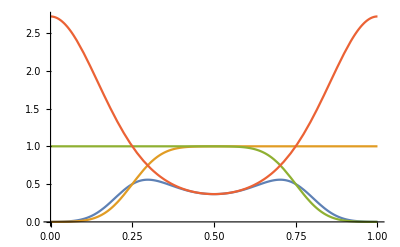

```mathematica
a=.1;
Plot[{W1s[x,a],(Erf[(x-.25)/a]+1)/2,(Erfc[(x-.75)/a])/2,Exp[Cos[2 π x]]},{x,0,1}]
```

```mathematica
Table[NIntegrate[W1s[x,i],{x,0,1}],{i,.01,.1,.01}]
```

{0.278226,0.279168,0.280738,0.282936,0.285759,0.289203,0.293261,0.297922,0.303168,0.308968}

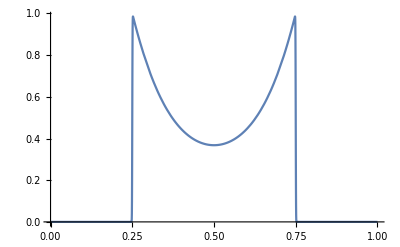
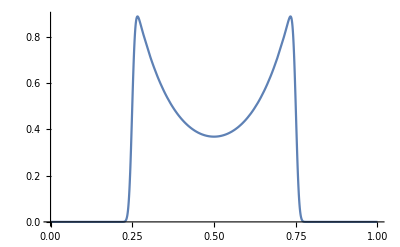
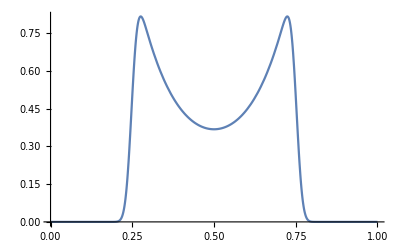
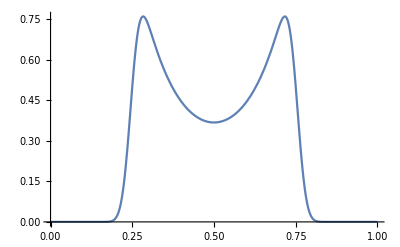
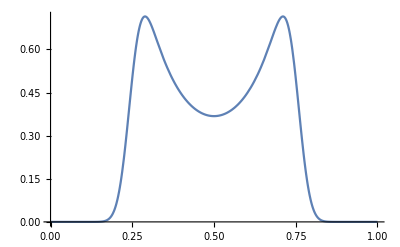
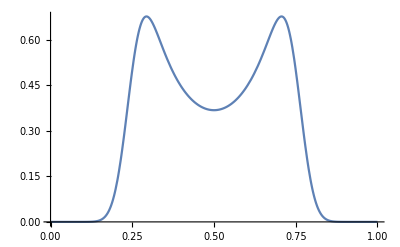
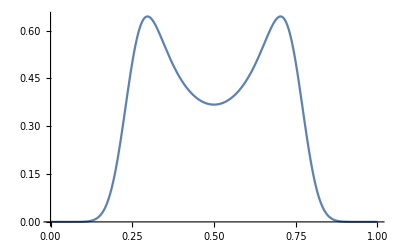
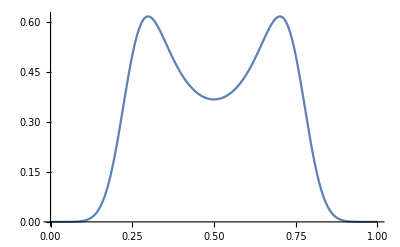

```mathematica
Table[Plot[W1s[x,i],{x,0,1}],{i,.001,.1,.01}]
```